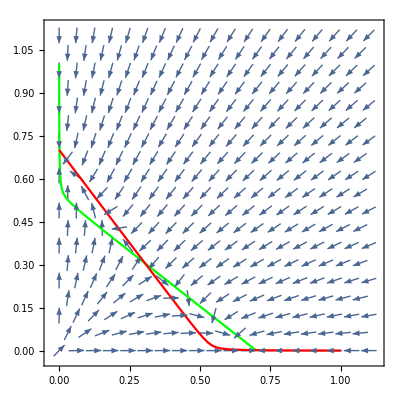

```mathematica
(*Parameter values*)

d=1; (*Normalized Dtot*)
ua=0.001;  (*basal and recruited de novo establishment for DA*)
ur=0.001; (*basal and recruited de novo establishment for DR*)
a=1; (*alpha*)

mu=1;
b=1;

e=0.3; (*epsilon*)

ee=0.3; (*epsilon'*)


(*Vector field and nullclines*)

vectorField = VectorPlot[{(ur+a*X1)*(d-X1-X2)-mu*(b*e+ee*X2)*X1,(ua+X2)*(d-X1-X2)-(e+ee*X1)*X2},{X1,0,1.1},{X2,0,1.1},
VectorStyle->Arrowheads[0.03],VectorPoints->19, VectorColorFunction->None];
nullclines2=ContourPlot[{X1==(-(-a*d+ur+mu*b*e+X2*(a+mu*ee))+((-a*d+ur+mu*b*e+X2*(a+mu*ee))^2-4*a*ur*(X2-d))^(1/2))/(2*a),X2==(-(-d+ua+e+X1*(1+ee))+((-d+ua+e+X1*(1+ee))^2-4*ua*(X1-d))^(1/2))/(2)},{X1,0,1.1},{X2,0,1.1},ContourStyle->{Green,Red}];
Show[vectorField,nullclines2]
```